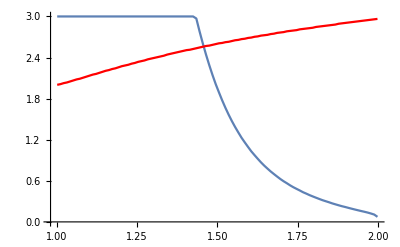

```mathematica
Clear["Global`*"];


numsig = 1000;
sigmin = 0.01; 
sigmax = Sqrt[4];
sigmavec = Table[s,{s, sigmin, sigmax, (sigmax - sigmin)/(numsig -1)}];

numr = 100;
rmin = 1.001; 
rmax = 2.1;
rvec = Table[r,{r, rmin, rmax, (rmax - rmin)/(numr -1)}];
critsigmavec = Table[r,{r, rmin, rmax, (rmax - rmin)/(numr -1)}];

critsigmavecopper = Table[r,{r, rmin, rmax, (rmax - rmin)/(numr -1)}];

Monitor[For[j=1, j<numr+1,j++,
r= rvec[[j]];
fvec = Table[0,{s, sigmin, sigmax, (sigmax - sigmin)/(numsig -1)}];
fvec2 = Table[0,{s, sigmin, sigmax, (sigmax - sigmin)/(numsig -1)}];
For[i = 1, i<numsig+1, i++,
sigma= sigmavec[[i]];
start = (1-1/r)^2 +0.2;
sol = FindRoot[1/(√(2 π) r^2)(ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √q (-1+r) r sigma-ⅇ^(-1/(2 q r^2 sigma^2)) √q r (-1+2 r) sigma-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q sigma)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r sigma)])+1/2 Erfc[1/(√2 √q r sigma)]==q,{q, start}];
q0 = q/.sol;

phi1 =(√q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2));
fvec[[i]] = NIntegrate[sigma^2 Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] r^2myx^2/((2 - r myx )^2),{myx, 0, 1}];(* +  phi1 r^2sigma^2/((2 - r )^2);*)
(*numsum =1000;
fvec[[i]] = Sum[sigma^2 Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] r^2myx^2/((2 - r myx )^2),{myx, 0, 1, 1/(numsum-1)}]*1/(numsum-1) +  phi1 r^2sigma^2/((1 - r )^2);*)
fvec2[[i]]=sigma^2(-Erf[(-1+1/r)/(√2 √q0 sigma)]+Erf[1/(√2 √q0 r sigma)])/2

];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
critsigmavec[[j]]= sigmavec[[pos]];

nearest = Nearest[fvec2,1][[1]];
pos = Position[fvec2, nearest][[1,1]];
critsigmavecopper[[j]]= sigmavec[[pos]];
];,j];



plt1 = ListLinePlot[Transpose[{ rvec,critsigmavec^2}], PlotRange->All];
plt2 = ListLinePlot[Transpose[{ rvec,critsigmavecopper^2}], PlotRange->All, PlotStyle->{Red}];
Show[plt1, plt2]
(*SetDirectory[NotebookDirectory[]];
Export["lambdavec.csv", critomvec]
Export["sigmavec.csv", sigmavec]
Export["critsigma.csv", critsigma]*)
```

```mathematica
(w12 w21) (w12s w21s)+u11 (-v22 w12s w21)
```